## Surface Acoustic Waves (with piezoelectric coupling): Analytical, perturbative solution

```mathematica
e14=0.15; (*units: C/m^2*)
ϵ0=8.85*10^(-12); (*F/m=C/Vm=C^2/(N*m^2)*)
ϵr=12.5;
ϵeff=ϵr*ϵ0;
echarge=1.6 10^(-19);
```

```mathematica
(*parameters for GaAs*)
c11Ga=12.26 10^(10); (*N/m^2*)
c12Ga=5.71 10^(10); (*N/m^2*)
c44Ga=6.00 10^(10); (*N/m^2*)
ρGa=5.307 10^(3);(*kg/m^3*)
c11bGa=1/2*(c11Ga+c12Ga+2*c44Ga);
ϵr=12.5;
r=1/ϵr;
```

```mathematica
(*parameters for Subscript[Al, x] Subscript[Ga, 1-x] As: interpolation for x=0.3 [Simon96]*)
c11Ga2=0.7*12.26*10^(10)+0.3*12.2*10^(10); (*N/m^2*)
c12Ga2=0.7*5.71*10^(10)+0.3*5.5*10^(10); (*N/m^2*)
c44Ga2=0.7*6*10^(10)+0.3*5.7*10^(10); (*N/m^2*)
ρGa2=0.7*5307+0.3*3598;(*kg/m^3*)c11bGa2=1/2*(c11Ga2+c12Ga2+2*c44Ga2);
ϵr=12.5;
r=1/ϵr;
```

Phase velocity GaAs

```mathematica
sol=Solve[(1-c11Ga/c44Ga X)((c11Ga*c11bGa-c12Ga^2)/c11Ga^2-X)^2== X^2*(c11bGa/c11Ga-X),{X}];
XGa=X/.sol[[1]];
vGa=Sqrt[c11Ga/ρGa*XGa]
```

2879.96

```mathematica
sol2=Solve[(1-c11Ga2/c44Ga2 X)((c11Ga2*c11bGa2-c12Ga2^2)/c11Ga2^2-X)^2== X^2*(c11bGa2/c11Ga2-X),{X}];
XGa2=X/.sol2[[1]];
vGa2=Sqrt[c11Ga2/ρGa2*XGa2]
```

3016.14

Dispersion relation GaAs

```mathematica
sol=Solve[(1-c11Ga/c44Ga X)((c11Ga*c11bGa-c12Ga^2)/c11Ga^2-X)^2== X^2*(c11bGa/c11Ga-X),{X}];
XGa1=X/.sol[[1]];
XGa2=X/.sol[[2]];
XGa3=X/.sol[[3]];
vGa1=Sqrt[c11Ga/ρGa*XGa1];
vGa2=Sqrt[c11Ga/ρGa*XGa2];
vGa3=Sqrt[c11Ga/ρGa*XGa3];
```

```mathematica
vGa1
vGa2
vGa3
(vGa3/vGa1)^2
```

2879.96

5515.67

6879.92

5.7068

```mathematica
ωGa1[k_]:= vGa1*k;
ωGa2[k_]:= vGa2*k;
ωGa3[k_]:= vGa3*k;
```

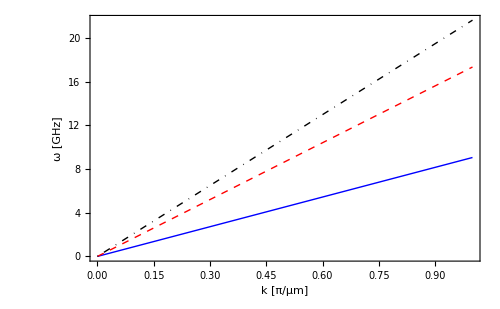

```mathematica
Plot[{10^(-9)*ωGa1[k*π*10^(6)],10^(-9)*ωGa2[k*π*10^(6)],10^(-9)*ωGa3[k*π*10^(6)]},{k,0,1},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick},{Red,Thick,Dashed},{Black,Thick,DotDashed},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["k [π/μm]",25]],Text[Style["ω [GHz]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

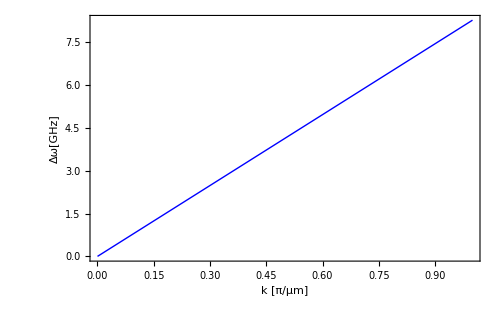

```mathematica
Plot[{10^(-9)*(ωGa2[k*π*10^(6)]-ωGa1[k*π*10^(6)])},{k,0,1},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick},{Red,Thick,Dashed},{Black,Thick,DotDashed},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["k [π/μm]",25]],Text[Style["Δω[GHz]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

Phase velocity GaP

```mathematica
(*parameters for GaAs*)
c11P=14.05 10^(10); (*N/m^2*)
c12P=6.2 10^(10); (*N/m^2*)
c44P=7.03 10^(10); (*N/m^2*)
ρP=4.138 10^(3);(*kg/m^3*)
c11bP=1/2*(c11P+c12P+2*c44P);
```

```mathematica
solP=Solve[(1-c11P/c44P X)((c11P*c11bP-c12P^2)/c11P^2-X)^2== X^2*(c11bP/c11P-X),{X}];
XP1=X/.solP[[1]];
XP2=X/.solP[[2]];
XP3=X/.solP[[3]];
vP1=Sqrt[c11P/ρP*XP1]
vP2=Sqrt[c11P/ρP*XP2]
vP3=Sqrt[c11P/ρP*XP3]
```

3532.3

6603.24

8711.31

```mathematica
m0=9.1 10^(-31); (*electron bare mass*)
melP=0.82*m0;
```

```mathematica
EsP=(melP/2)*vP1^2*10^6/echarge
```

29.0952

Decay constants

```mathematica
FullSimplify[Solve[(c44+(c11+c12)/2-ρ c^2-c44 *q^2)*(c44-ρ c^2-c11 q^2)+(c12+c44)^2*q^2== 0,{q}]]
```

{{q→-1/2 √(1/(c11 c44)(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44)-√(-8 c11 (-478440000000000000000+c44) c44 (-956880000000000000000+c11+c12+2 c44)+(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44))^2)))},{q→1/2 √(1/(c11 c44)(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44)-√(-8 c11 (-478440000000000000000+c44) c44 (-956880000000000000000+c11+c12+2 c44)+(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44))^2)))},{q→-1/2 √(1/(c11 c44)(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44)+√(-8 c11 (-478440000000000000000+c44) c44 (-956880000000000000000+c11+c12+2 c44)+(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44))^2)))},{q→1/2 √(1/(c11 c44)(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44)+√(-8 c11 (-478440000000000000000+c44) c44 (-956880000000000000000+c11+c12+2 c44)+(c11^2+c11 (-956880000000000000000+c12+2 c44)-2 (c12^2+2 (239220000000000000000+c12) c44))^2)))}}

```mathematica
q1n[c11_,c12_,c44_,ρ_,c_]:= -1/2 √(1/(c11 c44)(c11^2+c11 (c12+2 c44-2 c^2 ρ)-2 (c12^2+2 c12 c44+c^2 c44 ρ)-√(-8 c11 c44 (c11+c12+2 c44-2 c^2 ρ) (c44-c^2 ρ)+(c11^2+c11 c12-2 c12^2+2 c11 c44-4 c12 c44-2 c^2 (c11+c44) ρ)^2)));
q1p[c11_,c12_,c44_,ρ_,c_]:=1/2 √(1/(c11 c44)(c11^2+c11 (c12+2 c44-2 c^2 ρ)-2 (c12^2+2 c12 c44+c^2 c44 ρ)-√(-8 c11 c44 (c11+c12+2 c44-2 c^2 ρ) (c44-c^2 ρ)+(c11^2+c11 c12-2 c12^2+2 c11 c44-4 c12 c44-2 c^2 (c11+c44) ρ)^2)));
q2n[c11_,c12_,c44_,ρ_,c_]:= -1/2 √(1/(c11 c44)(c11^2+c11 (c12+2 c44-2 c^2 ρ)-2 (c12^2+2 c12 c44+c^2 c44 ρ)+√(-8 c11 c44 (c11+c12+2 c44-2 c^2 ρ) (c44-c^2 ρ)+(c11^2+c11 c12-2 c12^2+2 c11 c44-4 c12 c44-2 c^2 (c11+c44) ρ)^2)));
q2p[c11_,c12_,c44_,ρ_,c_]:=1/2 √(1/(c11 c44)(c11^2+c11 (c12+2 c44-2 c^2 ρ)-2 (c12^2+2 c12 c44+c^2 c44 ρ)+√(-8 c11 c44 (c11+c12+2 c44-2 c^2 ρ) (c44-c^2 ρ)+(c11^2+c11 c12-2 c12^2+2 c11 c44-4 c12 c44-2 c^2 (c11+c44) ρ)^2)));
```

```mathematica
q1p[c11Ga,c12Ga,c44Ga,ρGa,vGa]
q2p[c11Ga,c12Ga,c44Ga,ρGa,vGa]
q1n[c11Ga,c12Ga,c44Ga,ρGa,vGa]
q2n[c11Ga,c12Ga,c44Ga,ρGa,vGa]
```

0.49729-0.481904 ⅈ

0.49729+0.481904 ⅈ

-0.49729+0.481904 ⅈ

-0.49729-0.481904 ⅈ

```mathematica
q1p[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
q2p[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
q1n[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
q2n[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
```

0.50093-0.47221 ⅈ

0.50093+0.47221 ⅈ

-0.50093+0.47221 ⅈ

-0.50093-0.47221 ⅈ

Amplitude ratio

```mathematica
gamma1[c11_,c12_,c44_,ρ_,v_]:=(q1p[c11,c12,c44,ρ,v]*(c12+c44))/(c44-ρ*v^2-c11*q1p[c11,c12,c44,ρ,v]^2);
gamma2[c11_,c12_,c44_,ρ_,v_]:=(q2p[c11,c12,c44,ρ,v]*(c12+c44))/(c44-ρ*v^2-c11*q2p[c11,c12,c44,ρ,v]^2);
gamma1b[c11_,c12_,c44_,ρ_,v_]:=(c44*q1p[c11,c12,c44,ρ,v]^2+ρ*v^2-(c11+c12+2*c44)/2)/((c12+c44)*q1p[c11,c12,c44,ρ,v]);
gamma2b[c11_,c12_,c44_,ρ_,v_]:=(c44*q2p[c11,c12,c44,ρ,v]^2+ρ*v^2-(c11+c12+2*c44)/2)/((c12+c44)*q2p[c11,c12,c44,ρ,v]);
```

```mathematica
gamma1[c11Ga,c12Ga,c44Ga,ρGa,vGa]
gamma2[c11Ga,c12Ga,c44Ga,ρGa,vGa]
gamma1b[c11Ga,c12Ga,c44Ga,ρGa,vGa]
gamma2b[c11Ga,c12Ga,c44Ga,ρGa,vGa]
```

-0.682453-1.15518 ⅈ

-0.682453+1.15518 ⅈ

-0.682453-1.15518 ⅈ

-0.682453+1.15518 ⅈ

```mathematica
gamma1[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
gamma2[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
gamma1b[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
gamma2b[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]
```

-0.703537-1.14616 ⅈ

-0.703537+1.14616 ⅈ

-0.703537-1.14616 ⅈ

-0.703537+1.14616 ⅈ

Phase φ

```mathematica
z=-(gamma2[c11Ga,c12Ga,c44Ga,ρGa,vGa]*-q2p[c11Ga,c12Ga,c44Ga,ρGa,vGa]*)/(gamma2[c11Ga,c12Ga,c44Ga,ρGa,vGa]-q2p[c11Ga,c12Ga,c44Ga,ρGa,vGa]);
ϕGa=-Arg[z]/2
```

1.0522

```mathematica
z2=-(gamma2[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]*-q2p[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]*)/(gamma2[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]-q2p[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2]);
ϕGa2=-Arg[z2]/2
```

1.06066

Plot mechanical displacement

```mathematica
Ω=q2p[c11Ga,c12Ga,c44Ga,ρGa,vGa];
Γ=gamma2[c11Ga,c12Ga,c44Ga,ρGa,vGa];
ϕ=ϕGa;
uzSimon[x_,z_]:= -ⅈ(Γ*Exp[-2π Ω z-ⅈ ϕ]+Γ**Exp[-2π Ω* z+ⅈ ϕ])Exp[2π ⅈ x];
```

```mathematica
Ω2=q2p[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2];
Γ2=gamma2[c11Ga2,c12Ga2,c44Ga2,ρGa2,vGa2];
ϕ2=ϕGa2;
uzSimon2[x_,z_]:= -ⅈ(Γ2*Exp[-2π Ω2 z-ⅈ ϕ2]+Γ2**Exp[-2π Ω2* z+ⅈ ϕ2])Exp[2π ⅈ x];
```

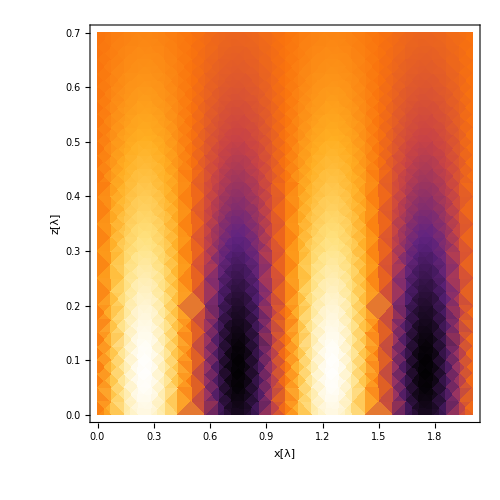

```mathematica
DensityPlot[Re[uzSimon[x,z]],{x,0,2},{z,0,0.7},ImageSize-> 500,FrameLabel->{Text[Style["x[λ]",25]],Text[Style["z[λ]",25]],Text[Style["u_z/U",25]],""},PlotRange-> All,FrameStyle->Directive[Black,25],ColorFunction->"SunsetColors"]
```

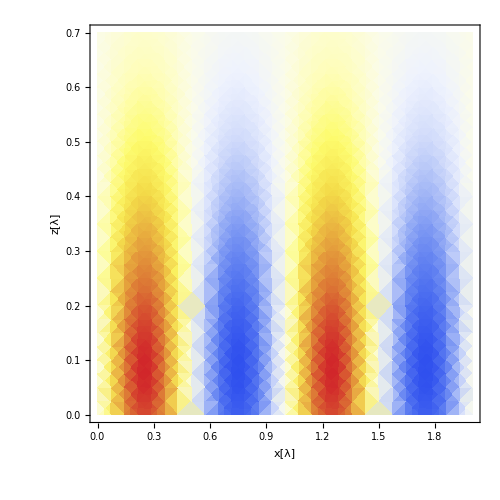

```mathematica
DensityPlot[Re[uzSimon[x,z]],{x,0,2},{z,0,0.7},ImageSize-> 500,FrameLabel->{Text[Style["x[λ]",25]],Text[Style["z[λ]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25],ColorFunction->"TemperatureMap"]
```

Dimensionless function ℱ: Decay of SAW into bulk

```mathematica
Γ2
Ω2
ϕ2
```

-0.703537+1.14616 ⅈ

0.50093+0.47221 ⅈ

1.06066

```mathematica
A1complex2=(Γ2-2Ω2)/(Ω2^2-1);
A1abs=Abs[A1complex2]
ξ=-Arg[A1complex2]
θ=ϕ2+ξ
```

1.58852

-0.335198

0.725461

```mathematica
θ-π
```

-2.41613

```mathematica
α=Re[Ω2]
β=Im[Ω2]
A3=-2/(1+r)*(Cos[ϕ2]+r*Re[A1complex2*Exp[-ⅈ ϕ2]]+Re[Ω2*A1complex2*Exp[-ⅈ ϕ2]])
```

0.50093

0.47221

-3.1045

```mathematica
F[qd_]:= 2*A1abs*Exp[-α*qd]*Cos[β*qd+θ]+A3*Exp[-qd];
f[qd_]:= 2*A1abs*Exp[-α*qd]*Cos[β*qd+2.41]+A3*Exp[-qd];
f2[qd_]:= 2*A1abs*Exp[-α*qd]*Sin[β*qd+2.41]+A3*Exp[-qd];
f3[qd_]:= -2*A1abs*Exp[-α*qd]*Cos[β*qd-2.41]+A3*Exp[-qd];
```

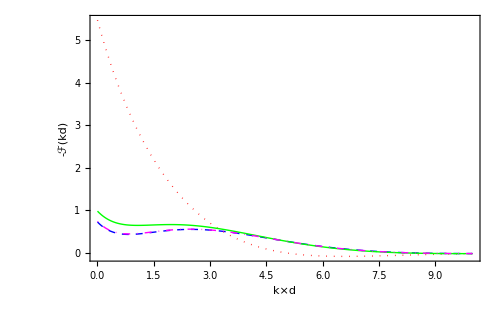

```mathematica
Plot[{-F[qd],-f[qd],-f2[qd],-f3[qd]},{qd,0,10},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick,Dashed},{Red,Thick,Dotted},{Green,Thick},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["k×d",25]],Text[Style["-ℱ(kd)",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

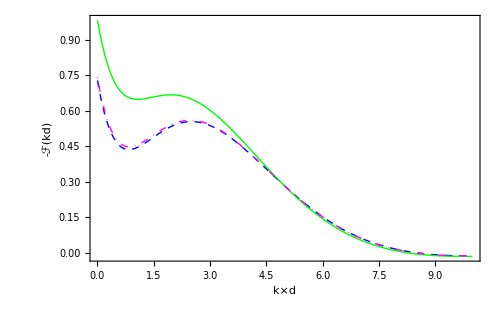

```mathematica
Plot[{-F[qd],-f2[qd],-f3[qd]},{qd,0,10},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick,Dashed},{Green,Thick},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["k×d",25]],Text[Style["-ℱ(kd)",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

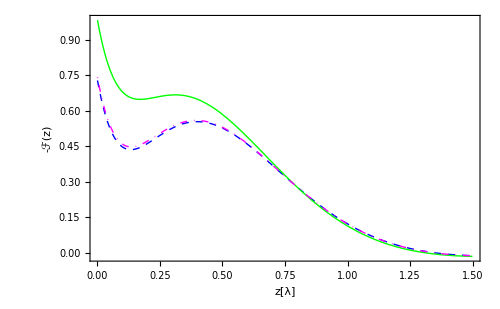

```mathematica
Plot[{-F[2π*z],-f2[2π*z],-f3[2π*z]},{z,0,1.5},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick,Dashed},{Green,Thick},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["z[λ]",25]],Text[Style["-ℱ(z)",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

```mathematica
(*comparison of my result (blue) with Eq.(51) in Simon96: Fig.2 in Simon96 behaviour is reproduced only with my parameter values*)
```

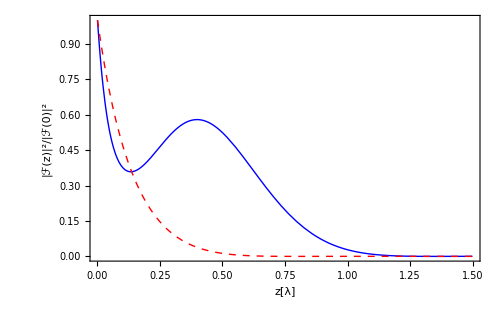

```mathematica
Plot[{F[2π*z]^2/F[0]^2, f[2π*z]^2/f[0]^2},{z,0,1.5},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick},{Red,Thick,Dashed},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["z[λ]",25]],Text[Style["|ℱ(z)|^2/|ℱ(0)|^2",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

```mathematica
ξs=2.41-1.06;
A1s=Abs[A1complex2]*Exp[-ⅈ*ξs]
A1m=Abs[A1complex2]*Exp[-ⅈ*ξ]
A1complex2
```

0.347896-1.54995 ⅈ

1.50011+0.522553 ⅈ

1.50011+0.522553 ⅈ

Plot electric potential generated by SAW

```mathematica
ΦSAWnorm[x_,z_]:= -F[2π z]*Sin[2π*x]
```

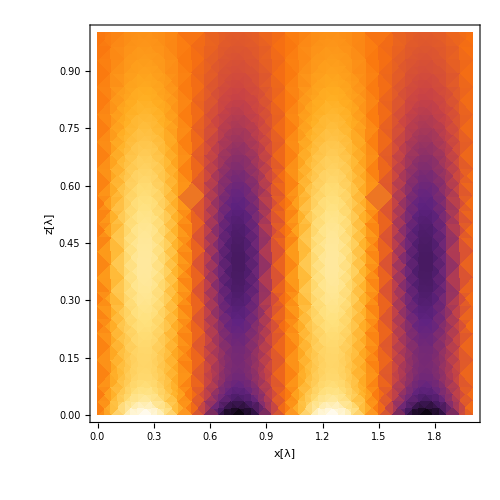

```mathematica
DensityPlot[Re[ΦSAWnorm[x,z]],{x,0,2},{z,0,1},ImageSize-> 500,FrameLabel->{Text[Style["x[λ]",25]],Text[Style["z[λ]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25],ColorFunction->"SunsetColors"]
```

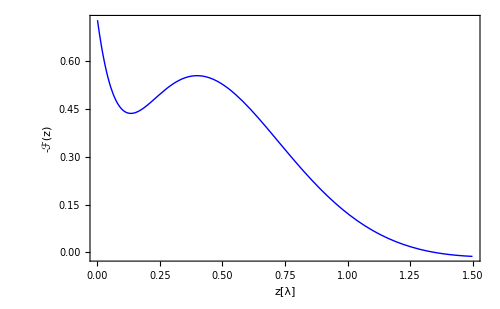

```mathematica
Plot[{-F[2π*z]},{z,0,1.5},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick},{Red,Thick,Dashed},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["z[λ]",25]],Text[Style["-ℱ(z)",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

Single phonon electric potential and electric field

```mathematica
CC=0.457;
ρ=5316;
vs=2863;
hbar= 1.054×10^(-34);(*units: J*s*)
hbarJ= hbar;(*units: J*s*)
hbarμeV=6.6 10^(-10); (*units: μeV*)
hplanck= 2π*hbar;(*units: J*s*)
```

```mathematica
ωph[ν_]:= 2π ν;
k[ν_]:=ωph[ν]/vs;
λ[ν_]:=2π/k[ν];
a[ν_]:=λ[ν]/2; (*lattice spacing*)
```

```mathematica
U0[ν_,L_]:= Sqrt[(2hbar*CC^2)/(ρ*vs)]*1/L;
E1ph[ν_,L_,qd_]:= Abs[(k[ν]*e14)/(ϵ0*ϵr)*F[qd]*U0[ν,L]];(*Electric field per single phonon, L^2 gives quantization area A*)ϕ1ph[ν_,L_,qd_]:= Abs[e14/(ϵ0*ϵr)*F[qd]*U0[ν,L]];
```

```mathematica
d=50*10^(-9); (*disance of QW from surface approx. 50nm*)
N[k[3*10^9]*d]
N[k[10*10^9]*d]
```

0.329192

1.09731

```mathematica
U0b[L_]:= Sqrt[(2hbar*CC^2)/(ρ*vs)]*1/L;
U0b[10^(-6)]
```

1.70078×10^-15

```mathematica
U0b[1*λ[3*10^9]]
U0b[1*λ[10*10^9]]
```

1.78217×10^-15

5.94055×10^-15

```mathematica
F[k[3*10^9]*d]
F[k[10*10^9]*d]
```

-0.519072

-0.446925

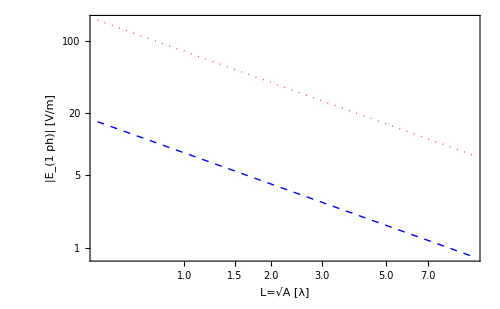

```mathematica
LogLogPlot[{E1ph[3*10^9,L*λ[3*10^9],k[3*10^9]*d],E1ph[10*10^9,L*λ[10*10^9],k[10*10^9]*d]},{L,0.5,10},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick,Dashed},{Red,Thick,Dotted}},FrameLabel->{Text[Style["L=√A [λ]",25]],Text[Style["|E_(1  ph)| [V/m]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

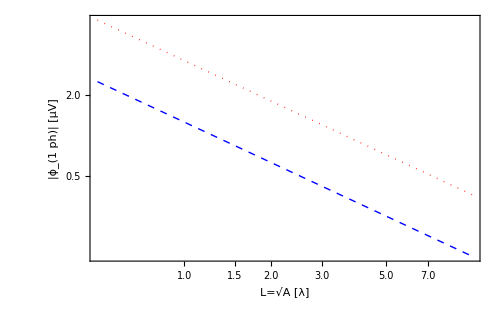

```mathematica
LogLogPlot[{10^6*ϕ1ph[3*10^9,L*λ[3*10^9],k[3*10^9]*d],10^6*ϕ1ph[10*10^9,L*λ[10*10^9],k[10*10^9]*d]},{L,0.5,10},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick,Dashed},{Red,Thick,Dotted}},FrameLabel->{Text[Style["L=√A [λ]",25]],Text[Style["|ϕ_(1  ph)| [μV]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

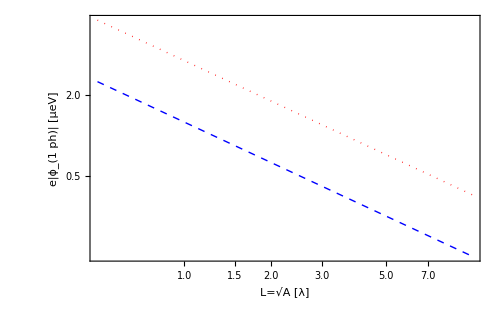

```mathematica
LogLogPlot[{10^6*ϕ1ph[3*10^9,L*λ[3*10^9],k[3*10^9]*d],10^6*ϕ1ph[10*10^9,L*λ[10*10^9],k[10*10^9]*d]},{L,0.5,10},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick,Dashed},{Red,Thick,Dotted}},FrameLabel->{Text[Style["L=√A [λ]",25]],Text[Style["e|ϕ_(1  ph)| [μeV]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

```mathematica
10^6*ϕ1ph[20*10^9,1*λ[20*10^9],k[20*10^9]*d]
```

8.80772

Single phonon electric potential and electric field for IONS above surface

```mathematica
(*trapping frequencies for ions are (10-50)MHz*)
```

```mathematica
dion=10*10^(-6); (*ions 10μm above the surface*)
νion=50*10^(6);
λion=N[λ[νion]]
λion*10^(6)(*in μm*)
dion/λion
```

0.00005726

57.26

0.174642

```mathematica
a0ion[mion_,ωtrap_]:= √(hbarJ/(2*mion*ωtrap));
atomicmass=1.66 10^(-27);
mBe=9*atomicmass;
a0ion[mBe,νion]
a0ion[mBe,2π*νion]
```

8.39934×10^-9

3.35085×10^-9

```mathematica
(*outside of material [red] electric potential decays faster than inside GaAs [gray]*)
```

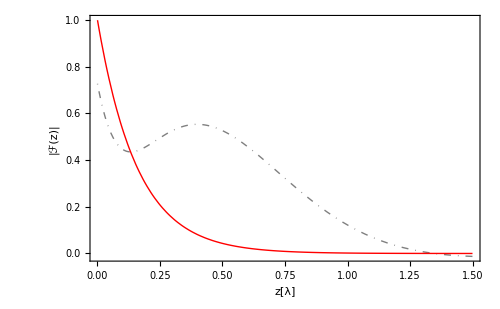

```mathematica
Plot[{-F[2π*z],Exp[-2π*z]},{z,0,1.5},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Gray,Thick,DotDashed},{Red,Thick},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["z[λ]",25]],Text[Style["|ℱ(z)|",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

```mathematica
N[k[νion]*dion]
F[k[νion]*dion]
N[Exp[-k[νion]*dion]]
N[Exp[-2π*dion/λion]]
```

1.09731

-0.446925

0.333768

0.333768

```mathematica
U0b[1*λ[νion]]
U0b[1*λion]
```

2.97028×10^-17

2.97028×10^-17

```mathematica
E1phIon[ν_,L_,qd_]:= Abs[(k[ν]*e14)/(ϵ0*ϵr)*F[0]*Exp[-2π*qd]*U0b[L]];(*Electric field per single phonon, L^2 gives quantization area A*)ϕ1phIon[L_,qd_]:= Abs[e14/(ϵ0*ϵr)*F[0]*Exp[-2π*qd]*U0b[L]];
E1phIon[ν_,L_,qd_]:= Abs[(k[ν]*e14)/(ϵ0*ϵr)*F[0]*Exp[-qd]*U0b[L]];(*Electric field per single phonon, L^2 gives quantization area A*)ϕ1phIon[L_,qd_]:= Abs[e14/(ϵ0*ϵr)*F[0]*Exp[-qd]*U0b[L]];
```

```mathematica
N[Exp[-2π*k[νion]*dion]]/N[Exp[-k[νion]*dion]]
```

0.0030358

```mathematica
10^6*ϕ1phIon[1*λ[νion],k[νion]*dion]
E1phIon[νion,1*λ[νion],k[νion]*dion]
10^6*ϕ1phIon[1*λ[νion],k[νion]*3*dion]
```

0.0097789

0.00107305

0.00108938

```mathematica
LambDickeIon=k[νion]*a0ion[mBe,νion]*10^(3)
LambDickeIon=k[νion]*a0ion[mBe,2π*νion]*10^(4)
```

0.921666

3.67692

```mathematica
gionμeV[mion_,ν_,L_,qd_]:=10^(6)*ϕ1phIon[L,qd]*k[ν]*a0ion[mion,2π*ν]; (*single phonon coupling strength to ion motion*)
gionJ[mion_,ν_,L_,qd_]:=echarge*ϕ1phIon[L,qd]*k[ν]*a0ion[mion,2π*ν];
gionHz[mion_,ν_,L_,qd_]:=gionμeV[mion,ν,L,qd]/hbarμeV;
gionkHz[mion_,ν_,L_,qd_]:=10^(-3)*gionμeV[mion,ν,L,qd]/hbarμeV;
```

```mathematica
gionμeV[mBe,νion,1*λ[νion],k[νion]*dion]
gionkHz[mBe,νion,1*λ[νion],k[νion]*dion]
gionkHz[mBe,νion,1*λ[νion],3*k[νion]*dion]
```

3.59562×10^-6

5.44791

0.606904

```mathematica
gionμeV[mBe,νion,1*λ[νion],k[νion]*dion]
gionkHz[mBe,νion,1*λ[νion],k[νion]*dion]
gionkHz[mBe,νion,1*λ[νion],3*k[νion]*dion]
```

3.59562×10^-6

5.44791

0.606904

```mathematica
(*For comparison: elec. potential due to SAW with GHz frequency coupled at d=50nm distance*)
10^(6)*ϕ1ph[3*10^9,λ[3*10^9],k[3*10^9]*d]
10^(6)*ϕ1ph[10*10^9,λ[10*10^9],k[10*10^9]*d]
```

1.25433

3.59997

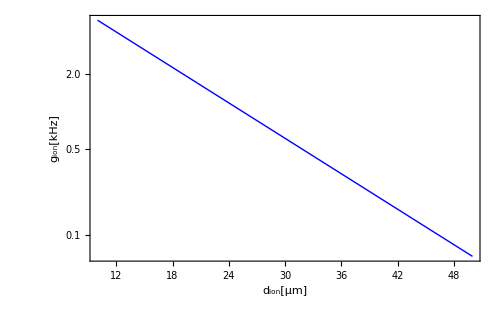

```mathematica
LogPlot[{gionkHz[mBe,νion,1*λ[νion],k[νion]*dion*10^(-6)]},{dion,10,50},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick},{Magenta,Thick,DotDashed}},FrameLabel->{Text[Style["d_ion[μm]",25]],Text[Style["g_ion[kHz]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

```mathematica
gionkHz[mBe,νion,1*λ[νion],k[νion]*10*10^(-6)]
```

5.44791

```mathematica
gionkHz[mBe,νion,1*λ[νion],k[νion]*30*10^(-6)]
```

0.606904

Motional Decoherence Rate for IONS: PRL 108, 130504 (2012)

```mathematica
γmotionaldecoherencekHz[dion_]:= 10^(-3)*0.5*((150 10^(-6))/dion)^4;
```

```mathematica
γmotionaldecoherencekHz[25 10^(-6)]
γmotionaldecoherencekHz[30 10^(-6)]
```

0.648

0.3125

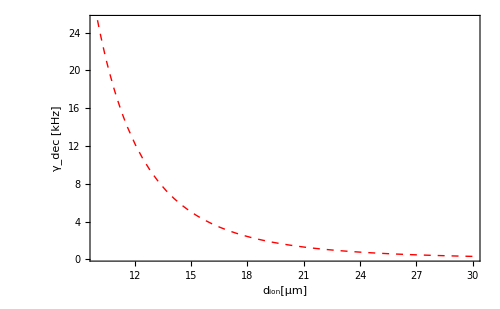

```mathematica
Plot[{γmotionaldecoherencekHz[dion*10^(-6)]},{dion,10,30},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Red,Thick,Dashed},{Red,Thick,Dashed}},FrameLabel->{Text[Style["d_ion[μm]",25]],Text[Style["γ_dec [kHz]",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

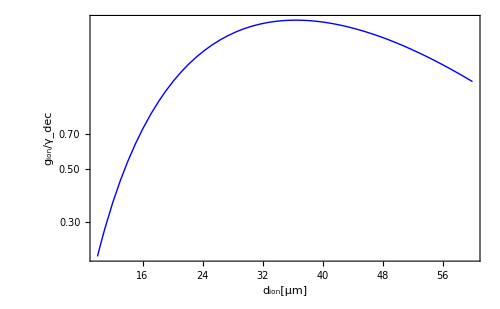

```mathematica
LogPlot[{gionkHz[mBe,νion,1*λ[νion],k[νion]*dion*10^(-6)]/γmotionaldecoherencekHz[dion*10^(-6)]},{dion,10,60},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick},{Red,Thick,Dashed}},FrameLabel->{Text[Style["d_ion[μm]",25]],Text[Style["g_ion/γ_dec",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

Single-spin cooperativity for IONS

```mathematica
ℏωμeV[ω_]:= hbarμeV*ω;(*frequency in μeV*)
kB=8.6 10^(-5)*10^(6); (*units: μeV/K*)
EthermalμeV[T_]:= kB*T; 
Nth[ω_,T_]:= 1/(Exp[ℏωμeV[ω]/EthermalμeV[T]]-1);
```

```mathematica
ηcoopion[mion_,ν_,L_,qd_,d_,Q_,ωSAW_]:= (gionHz[mion,ν,L,qd]^2*Q)/((10^(3)*γmotionaldecoherencekHz[d])*ωSAW);
ηcoopionTemp[mion_,ν_,L_,qd_,d_,Q_,ωSAW_,T_]:= (gionHz[mion,ν,L,qd]^2*Q)/((10^(3)*γmotionaldecoherencekHz[d])*ωSAW*(Nth[ωSAW,T]+1));
```

```mathematica
Nth[2π *50 10^(6),10 10^(-3) ]
```

3.66775

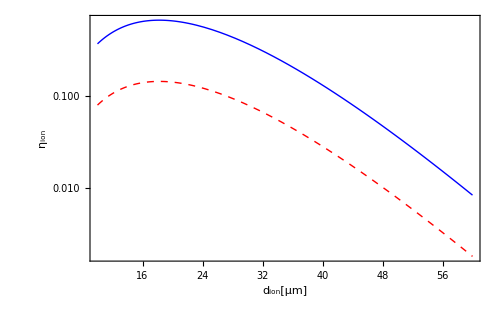

```mathematica
LogPlot[{ηcoopion[mBe,νion,1*λ[νion],k[νion]*dion*10^(-6),dion*10^(-6),10^5,2π*νion],ηcoopionTemp[mBe,νion,1*λ[νion],k[νion]*dion*10^(-6),dion*10^(-6),10^5,2π*νion,10 10^(-3)]},{dion,10,60},Frame-> True,Axes-> None,ImageSize-> 500,PlotStyle-> {{Blue,Thick},{Red,Thick,Dashed}},FrameLabel->{Text[Style["d_ion[μm]",25]],Text[Style["η_ion",25]],"",""},PlotRange-> All,FrameStyle->Directive[Black,25]]
```

```mathematica
ηcoopionTemp[mBe,νion,1*λ[νion],k[νion]*20*10^(-6),20*10^(-6),10^5,2π*νion,10 10^(-3)]
```

0.142521